# Dynamic Topology Neural Networks

## Phileas Dazeley-Gaist

```mathematica
SystemOpen@NotebookDirectory[]
```

### Misc notes

Tasks to try:

Mimicry: Get the neural network to reproduce a function, and verify that the function was actually learned.

Open-ended learning: Get the neural network to solve a problem according to its own chosen rule through evolution and adaptation.

Hebbian learning.

environment

(I am assuming the neurons are named with positive integers in sequence)

-Graphics-

A single classic artificial neuron:

```mathematica
With[{x={0,1,0,1,0},w=RandomReal[1,5],b=0,activationFunction=Sin},activationFunction[Total[x*w+b]]]
```

0.813899

```mathematica
(*With[{w=RandomReal[1,5],b=0,activationFunction=Sin},activationFunction[Total[x*w+b]]]*)
```

```mathematica
(*Generate the neuron function*)(*With[{w=RandomReal[1,5],b=0,activationFunction=Sin},Function[x,activationFunction[Total[x*w+b]]]]*)
```

## Initialisation logic

### Initial tests

Base network structure:

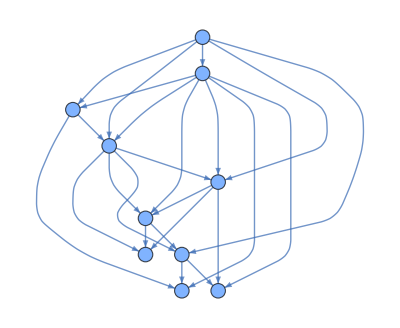

```mathematica
g=With[{v=10},Graph[Range[v],DirectedEdge@@@EdgeList[RandomGraph[BarabasiAlbertGraphDistribution[v,3]]],VertexSize->Large]]
```

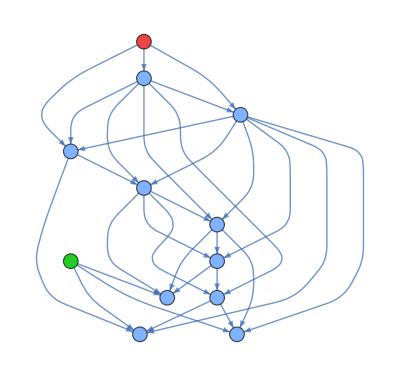

```mathematica
EdgeAdd[g,{"in"->1,"in"->2,"in"->3,"out"->8,"out"->9,"out"->10},VertexStyle->{"in"->StandardRed,"out"->StandardGreen}]
```

Generate random initial edge weights from a chosen statistical distribution:

```mathematica
ClearAll[initializeEdgeWeights]
initializeEdgeWeights[g_Graph,distribution_:NormalDistribution[0,0.11]]:=
	With[{adj=AdjacencyMatrix[g]},adj*RandomVariate[distribution,Dimensions[adj]]]
```

```mathematica
(*initW=initializeEdgeWeights[g]
%//ArrayPlot[#,ImageSize->Tiny]&*)
```

Fan-in normalization (initial penalty to higher degree nodes):

```mathematica
ClearAll[fanInNormalize]
fanInNormalize[vertexDegrees_List,weights_?ArrayQ,scalingFunction_:(*Xavier/He initialization*)Sqrt]:=
	SparseArray[MapIndexed[1/scalingFunction[Max[Extract[vertexDegrees,#2],1]]*#1&,weights]]
```

```mathematica
(*fanInNormalize[VertexDegree[g],initW]
%//ArrayPlot[#,ImageSize->Tiny]&*)
```

### Neural network state representation

```mathematica
ClearAll[neuralNet]

Options[neuralNet]={"Biases"->0,"SensorySensitivity"->1,"SensoryInput"->0,"MaxDensity"->.5};

neuralNet[network_Graph/;VertexList[network]===Range[VertexCount[network]],OptionsPattern[]]:=AssociationThread[
	{"network","weights","biases","activation",(*"networkSkeleton",*)"sensorySensitivity","sensoryInput","maxDensity"},
	{network,
	(*Initial weights are random gaussian variables around zero:*)
	fanInNormalize[VertexDegree[network],initializeEdgeWeights[network]],
	(*Initial bias is 0:*)OptionValue["Biases"],
	(*Initial activations are either zero or noise:*)(*Table[0,VertexCount[network]]*)RandomVariate[NormalDistribution[0,.25],VertexCount[network]],
	(*(*The network skeleton is the the adjacency matrix of the network:*)AdjacencyMatrix[network],*)
	(*Default sensory sensitivity is 1/1 signal received to signal perceived for all neurons:*)OptionValue["SensorySensitivity"],
	(*Default sensory input is 0:*)0,
	(*Default density is .5:*)OptionValue["MaxDensity"]
	}]
	
neuralNet[g_Graph]:=Failure["BadGraph",<|"MessageTemplate"->"The graph g has incorrectly indexed vertices."|>]
```

```mathematica
sampleBrain=neuralNet[g]
```

<|network→-Graphics-,weights→SparseArray[…],biases→0,activation→{-0.200179,0.0209945,-0.112098,-0.122883,-0.0858993,0.380615,-0.21078,-0.059275,0.172771,0.469359},sensorySensitivity→1,sensoryInput→0,maxDensity→0.5|>

```mathematica
(*Dataset[sampleBrain][<|#,"weights"->AdjacencyGraph[Map[If[Positive[Abs[#]],1,0]&,#weights,{2}]],"networkSkeleton"->EchoFunction["EdgeCount",EdgeCount]@AdjacencyGraph[#networkSkeleton]|>&]*)
```

## Transition function

The transition  is composed of three sequential phases.

### The pulse

Calculate the internal pre-activation using a dot product for recurrence and a Hadamard product for sensory input:

Update activation via leaky integration:

Note that  represents the signal flowing from neighbors through existing synapses.

Compute the pre-activation of

```mathematica
ClearAll[preActivation]
preActivation[brainState_Association]:=(brainState["weights"].brainState["activation"])+
	(brainState["sensorySensitivity"]*brainState["sensoryInput"])+brainState["biases"]
```

```mathematica
(*preActivation[sampleBrain]*)
```

Update activation via leaky integration:

```mathematica
ClearAll[updateActivations]
updateActivations[brainState_Association,Optional[leakRate_?NumericQ,.1],activationFunction_:Tanh]:=<|#,
	"activation"->(1-leakRate)#activation+leakRate*activationFunction[preActivation[#]]|>&@brainState
```

```mathematica
(*updateActivations[sampleBrain]*)
```

### The trace

The “trace” is the physiological record of the pulse. We use a Reward-Modulated Oja’s Rule to update weights. Oja’s rule is a stabilised form of Hebbian learning that prevents weight explosion.

Hebbian Term (): Strengthens connections between co-active neurons (“Fire together, wire together”).

Oja Stabiliser (): Acts as a metabolic governor. It forces neurons to “compete” for synaptic strength; as one connection strengthens, others are slightly taxed.

Gating (): If the environment provides no reward (e.g., the Ant is wandering),  and the physiology remains static.

Local learning (Hebbian) with Oja’s rule:

```mathematica
ClearAll[ojaUpdate]
ojaUpdate[weights_?ArrayQ,activation_List]:=(*Hebbian learning:*)Outer[Times,activation,activation]-(*Oja stabilisation:*)(activation^2 weights)
```

```mathematica
(*ojaUpdate[sampleBrain["weights"],(*RandomReal[1,VertexCount[g]]*)sampleBrain["activation"]]*)
```

Trace:

```mathematica
(*ClearAll[adaptWeights]
adaptWeights[brainState_Association,Optional[rewardSignal_?NumericQ,0],Optional[learningRate_?NumericQ,.01]]:=<|#,
	"weights"->Clip[#networkSkeleton(#weights+(rewardSignal*learningRate*ojaUpdate[#weights,#activation]))]|>&@brainState*)	

ClearAll[adaptWeights]
adaptWeights[brainState_Association,Optional[rewardSignal_?NumericQ,0],Optional[learningRate_?NumericQ,.01]]:=<|#,
	"weights"->Clip[AdjacencyMatrix[#network](#weights+(rewardSignal*learningRate*ojaUpdate[#weights,#activation]))]|>&@brainState
```

```mathematica
(*adaptWeights[sampleBrain,1,.01]*)
```

### The selection

Selection is the discrete, metabolic step where the physical mask  is re-evaluated. This occurs either every tick or at a lower frequency .

Pruning (Synaptic Death):

Synapses require metabolic maintenance. If a connection fails to prove its functional utility (its causal weight is too low), it is discarded to save resources.

Criteria: If , the synapse is marked for death.
Operation:  and .

Effect: This clears “physiological noise” and ensures the graph remains sparse, allowing the network to focus its energy on high-signal pathways.

Sprouting (Synaptic Birth)

The network explores potential connections by monitoring “latent correlations”—pairs of neurons that fire together despite having no physical connection.

Criteria: Identify pairs  where  AND the instantaneous correlation  (Sprouting Threshold).
Operation:  and  (Pioneer Weight).

Pioneer Weight (): A tiny, positive seed value. This allows the new connection to enter the “Trace” phase in the next tick and grow if the correlation persists.

Metabolic Budgeting ()

To prevent the graph from becoming a dense, all-to-all matrix (which destroys the causal benefits of topology), we enforce a hard limit on total edges: .

The “One-In, One-Out” Protocol: If the network is at its metabolic capacity ($|E| = E_{max}$) and seeks to sprout a new edge, it must first prune the weakest existing edge in the entire system, regardless of whether that edge is below .

Implication: This creates a zero-sum competitive ecosystem where new exploratory structures must “earn” their place by displacing the least useful existing ones.

#### Pruning (synaptic death)

Prune weak synapses:

```mathematica
(*ClearAll[pruneSynapses]
pruneSynapses[brainState_Association,Optional[survivalThreshold_?NumericQ,.005]]:=With[
	{survivalMask=UnitStep[Abs[brainState["weights"]]-survivalThreshold]},
	<|#,"network"->AdjacencyGraph[VertexList[#network],survivalMask],"weights"->#weights*survivalMask,"networkSkeleton"->survivalMask|>&@brainState]*)
	
ClearAll[pruneSynapses]
pruneSynapses[brainState_Association,Optional[survivalThreshold_?NumericQ,.005]]:=With[
	{survivalMask=UnitStep[Abs[brainState["weights"]]-survivalThreshold]},
	<|#,"network"->AdjacencyGraph[VertexList[#network],survivalMask],"weights"->#weights*survivalMask(*,"networkSkeleton"->survivalMask*)|>&@brainState]
```

```mathematica
(*Dataset[pruneSynapses[sampleBrain,.005]][<|#,"weights"->AdjacencyGraph[Map[If[Positive[Abs[#]],1,0]&,#weights,{2}]],"networkSkeleton"->EchoFunction["EdgeCount",EdgeCount]@AdjacencyGraph[#networkSkeleton]|>&]*)
```

#### Sprouting (synaptic birth)

The network explores potential connections by monitoring “latent correlations”—pairs of neurons that fire together despite having no physical connection.

Criteria: Identify pairs  where  AND the instantaneous correlation  (Sprouting Threshold).
Operation:  (Pioneer Weight).

Pioneer Weight (): A tiny, positive seed value. This allows the new connection to enter the “Trace” phase in the next tick and grow if the correlation persists.

Compute the potentiality matrix:

```mathematica
(*ClearAll[potentialityMatrix]
potentialityMatrix[brainState_]:=With[
	{nonEdgeMask=1-brainState["networkSkeleton"]-IdentityMatrix[VertexCount[brainState["network"]]]},
	nonEdgeMask*Outer[Times,brainState["activation"],brainState["activation"]]]*)
	
ClearAll[potentialityMatrix]
potentialityMatrix[brainState_]:=With[
	{nonEdgeMask=1-AdjacencyMatrix[brainState["network"]]-IdentityMatrix[VertexCount[brainState["network"]]]},
	nonEdgeMask*Outer[Times,brainState["activation"],brainState["activation"]]]
```

```mathematica
(*Round[potentialityMatrix[sampleBrain],.01]*)
```

Sprout new synapses:

```mathematica
(*ClearAll[sproutSynapses];
sproutSynapses[brainState_Association,Optional[sproutingRate_?NumericQ,1],Optional[sproutingThreshold_?NumericQ,.1],weightAssignmentFunction_:(0.001&)]:=Module[{w,net,n,maxEdges,rawCandidates,currentEdgeCount,overflow,gladiators,arena,survivors,toAdd,toKill,newW,newNet},newW=brainState["weights"];
	newNet=brainState["network"];
	n=Length[brainState["activation"]];
	(*1. Calculate Ceiling*)
	maxEdges=Ceiling[brainState["maxDensity"]*n^2];
	(*2. Identify Candidates (The Void)*)(*Using Normal[] to ensure we map over zeros correctly*)rawCandidates=Select[Flatten[MapIndexed[{#2,#1}&,Normal[(#*UnitStep[#])&@(potentialityMatrix[brainState]-sproutingThreshold)],{2}],1],Positive[Last[#]]&];
	(*SAFE FILTERING:Handle asking for more than exist*)
	If[Length[rawCandidates]>sproutingRate,rawCandidates=TakeLargestBy[rawCandidates,Last,sproutingRate];];
	If[Length[rawCandidates]===0,Return[brainState]];
	(*3. The Arena Logic*)currentEdgeCount=EdgeCount[newNet];
	overflow=Max[0,(currentEdgeCount+Length[rawCandidates])-maxEdges];
	If[overflow>0,
	(*Find Gladiators*)gladiators=Map[{First[#],Abs[Last[#]]}&,TakeSmallestBy[Select[ArrayRules[newW],Last[#]!=0&],Abs[Last[#]]&,overflow]];
	(*The Duel*)arena=Join[rawCandidates,gladiators];
	(*Safe TakeLargest for survivors*)survivors=If[Length[arena]>Length[rawCandidates],TakeLargestBy[arena,Last,Length[rawCandidates]],arena];
	(*Sort bodies*)toAdd=Select[survivors,MemberQ[rawCandidates,#]&];
	(*Fix:Ensure we match on indices only for killing*)toKill=Select[gladiators,!MemberQ[First/@survivors,First[#]]&];,(*Under Budget*)toAdd=rawCandidates;
	toKill={};];
	(*4. Execute Updates*)
	(*Prune*)If[Length[toKill]>0,newW=ReplacePart[newW,(First/@toKill)->0.];
	newNet=EdgeDelete[newNet,DirectedEdge@@@(First/@toKill)];];
	(*Sprout*)If[Length[toAdd]>0,newNet=EdgeAdd[newNet,DirectedEdge@@@(First/@toAdd)];
	newW=newW+SparseArray[Thread[(First/@toAdd)->Map[weightAssignmentFunction,Last/@toAdd]],Dimensions[newW]];];
	<|brainState,"network"->newNet,"weights"->newW,"networkSkeleton"->AdjacencyMatrix[newNet]|>]*)
	
ClearAll[sproutSynapses];
sproutSynapses[brainState_Association,Optional[sproutingRate_?NumericQ,1],Optional[sproutingThreshold_?NumericQ,.1],weightAssignmentFunction_:(0.001&)]:=Module[{w,net,n,maxEdges,rawCandidates,currentEdgeCount,overflow,gladiators,arena,survivors,toAdd,toKill,newW,newNet},newW=brainState["weights"];
	newNet=brainState["network"];
	n=Length[brainState["activation"]];
	(*1. Calculate Ceiling*)
	maxEdges=Ceiling[brainState["maxDensity"]*n^2];
	(*2. Identify Candidates (The Void)*)(*Using Normal[] to ensure we map over zeros correctly*)rawCandidates=Select[Flatten[MapIndexed[{#2,#1}&,Normal[(#*UnitStep[#])&@(potentialityMatrix[brainState]-sproutingThreshold)],{2}],1],Positive[Last[#]]&];
	(*SAFE FILTERING:Handle asking for more than exist*)
	If[Length[rawCandidates]>sproutingRate,rawCandidates=TakeLargestBy[rawCandidates,Last,sproutingRate];];
	If[Length[rawCandidates]===0,Return[brainState]];
	(*3. The Arena Logic*)currentEdgeCount=EdgeCount[newNet];
	overflow=Max[0,(currentEdgeCount+Length[rawCandidates])-maxEdges];
	If[overflow>0,
	(*Find Gladiators*)gladiators=Map[{First[#],Abs[Last[#]]}&,TakeSmallestBy[Select[ArrayRules[newW],Last[#]!=0&],Abs[Last[#]]&,overflow]];
	(*The Duel*)arena=Join[rawCandidates,gladiators];
	(*Safe TakeLargest for survivors*)survivors=If[Length[arena]>Length[rawCandidates],TakeLargestBy[arena,Last,Length[rawCandidates]],arena];
	(*Sort bodies*)toAdd=Select[survivors,MemberQ[rawCandidates,#]&];
	(*Fix:Ensure we match on indices only for killing*)toKill=Select[gladiators,!MemberQ[First/@survivors,First[#]]&];,(*Under Budget*)toAdd=rawCandidates;
	toKill={};];
	(*4. Execute Updates*)
	(*Prune*)If[Length[toKill]>0,newW=ReplacePart[newW,(First/@toKill)->0.];
	newNet=EdgeDelete[newNet,DirectedEdge@@@(First/@toKill)];];
	(*Sprout*)If[Length[toAdd]>0,newNet=EdgeAdd[newNet,DirectedEdge@@@(First/@toAdd)];
	newW=newW+SparseArray[Thread[(First/@toAdd)->Map[weightAssignmentFunction,Last/@toAdd]],Dimensions[newW]];];
	<|brainState,"network"->newNet,"weights"->newW(*,"networkSkeleton"->AdjacencyMatrix[newNet]*)|>]
```

```mathematica
(*sproutSynapses[<|sampleBrain,"maxDensity"->1|>,4,1]*)
```

```mathematica
(*sproutSynapses[<|sampleBrain,"maxDensity"->1|>,100,.01]*)
```

```mathematica
(*Dataset[sproutSynapses[sampleBrain,10,.1]][<|#,"weights"->AdjacencyGraph[Map[If[Positive[Abs[#]],1,0]&,Normal[#weights],{2}]],"networkSkeleton"->EchoFunction["EdgeCount",EdgeCount]@AdjacencyGraph[#networkSkeleton]|>&]*)
```

Note: if sproutingRate is larger than the number of candidates that actually pass the threshold, the function will just return the list of all candidates that passed.

### Simulation loop

Proof of concept:

```mathematica
(*sampleBrain//updateActivations//adaptWeights//pruneSynapses//sproutSynapses*)
```

Compute the next simulation step function:

```mathematica
ClearAll[step]
Options[step]={
	"LeakRate"->.1,
	"ActivationFunction"->Tanh,
	"LearningRate"->0.01,
	"SurvivalThreshold"->.005,
	"SproutingRate"->1,
	"SproutingThreshold"->.1,
	"WeightAssignmentFunction"->(.001&)};

step[brainState_Association,Optional[sensoryInput_,0],Optional[rewardSignal_?NumericQ,1],OptionsPattern[]]:=
	sproutSynapses[
		pruneSynapses[
			adaptWeights[
				updateActivations[
					Append[brainState,"sensoryInput"->sensoryInput],
					OptionValue["LeakRate"],OptionValue["ActivationFunction"]],
				rewardSignal,OptionValue["LearningRate"]],
			OptionValue["SurvivalThreshold"]
			],
		OptionValue["SproutingRate"],OptionValue["SproutingThreshold"],OptionValue["WeightAssignmentFunction"]
		]/;Or[ListQ[sensoryInput],NumericQ[sensoryInput]]
```

Example:

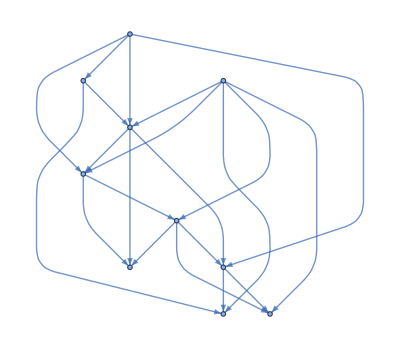
<|network→-Graphics-,weights→SparseArray[…],biases→0,activation→{-0.105288,0.095098,-0.0247858,-0.0352154,0.000385938,0.41912,-0.113515,0.0228119,0.231653,0.498582},sensorySensitivity→1,maxDensity→0.5,sensoryInput→1|>

```mathematica
step[sampleBrain,1,1]
```

Compute multiple steps:

```mathematica
(*Nest[step[#,0,0]&,sampleBrain,10]*)
```

```mathematica
(*Dataset[FoldList[step[#1,#2,1]&,sampleBrain,{1,1,1}]]*)
```

## Short-term dynamics:

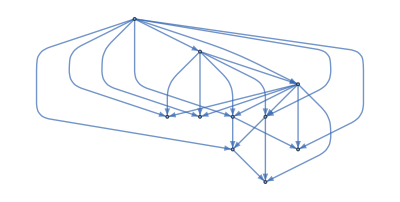
<|network→-Graphics-,weights→SparseArray[…],biases→0,activation→{-0.153382,-0.264288,0.258008,0.148188,-0.384736,-0.170678,-0.239502,-0.151638,0.235289,0.368236},sensorySensitivity→1,sensoryInput→0,maxDensity→0.5|>

```mathematica
ClearAll[brain]
(*Initialize a brain with a Barabasi Albert graph with the specified parameters:*)
brain=With[{n=10,k=3,τ=.005},
neuralNet[
(*Generate a Barabasi Albert graph with the chosen parameters:*)
RandomGraph[BarabasiAlbertGraphDistribution[n,k]]//
(*Convert edges to directed edges and indexed vertices::*)
(Graph[Sort[VertexList[#]],MapApply[DirectedEdge,#]]&@EdgeList[#]&)//
(*Delete any existing edges between node 1 and node n:*)
EdgeDelete[#,_?(MatchQ[#,1->n|n->1]&)]&
]]
```

The supposed complete state configuration table is: (generated by Gemini; to check manually at some point)

```mathematica
stateConfigTable=Tabular[Rest[#],First[#]]&@
```

### Sensory input = 0 (silence)

#### Reward = 0 (metabolic decay)

If I feed the brain no sensory input and no reward, the existing weights don’t undergo Hebbian learning, but the metabolism continues to run, so neuron activations leak at the specified LeakRate, edges whose weights are under the SurvivalThreshold are pruned, and vertices whose residual activations correlate sprout new connections at the specified SproutingRate within the MaxDensity capacity.

We can simulate these conditions with:

```mathematica
Nest[step[#,0,0]&,brain,10];
```

If the brain has residual neural activity, it fades at LeakRate:

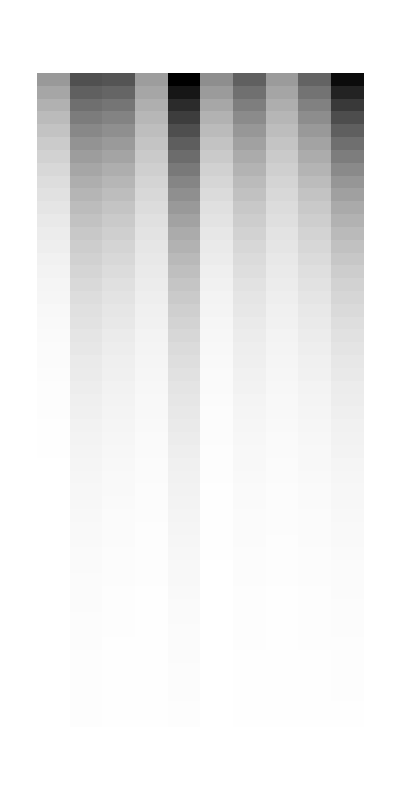

```mathematica
Dataset[NestList[step[#,0,0]&,brain,50]][All,#"activation"&][ArrayPlot[#,AspectRatio->2,ImageSize->Tiny]&]
```

Because under this regime, weights can only change as a result of pruning or sprouting, and the

```mathematica
Dataset[NestList[step[#,0,0]&,brain,50]][{1,-1},"weights"][Diff@@Normal[#]&]
```

```mathematica
Dataset[NestList[step[#,0,0]&,brain,50]][{1,-1},ArrayPlot[#"weights",PlotLegends->Automatic]&][Labeled[#1,"Start",Top]->Labeled[#2,"Finish",Top]&@@##&]
```

-Graphics-Start→-Graphics-Finish

#### Reward = 1 (hallucination) TODO[CHECK]

If I feed the brain no sensory input, but a strong positive reward, any residual activity will trigger a positive feedback loop. If this reinforcement strengthens weights faster than the signal decays, internal echoes will amplify and overcome the metabolic LeakRate, causing self-reinforcing loops to dominate while inactive edges are displaced by competitive replacement, and vertices whose consequently saturated activations correlate are added at the specified SproutingRate within the capacities of the graph as specified by MaxDensity. The system effectively learns its own noise.

Example:

```mathematica
(*Nest[step[#,0,1]&,brain,10]*)
```

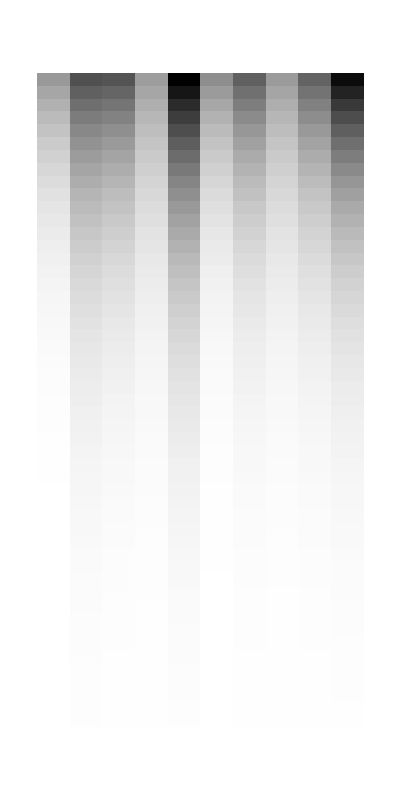

```mathematica
Dataset[NestList[step[#,0,1]&,brain,50]][All,#"activation"&][ArrayPlot[#,AspectRatio->2,ImageSize->Tiny]&]
```

```mathematica
Dataset[NestList[step[#,0,1]&,brain,50]][{1,-1},ArrayPlot[#"weights",PlotLegends->Automatic]&][Labeled[#1,"Start",Top]->Labeled[#2,"Finish",Top]&@@##&]
```

-Graphics-Start→-Graphics-Finish

#### Reward = -1 (self-destruction) TODO[CHECK]

If I feed the brain no sensory input and give a strong negative reward, the existing weights involved in residual activity are actively decreased, neuron activations leak to zero at the specified LeakRate, edges are rapidly pruned as they fall under the SurvivalThreshold, and sprouting is suppressed as new correlations are immediately punished within the capacities of the graph as specified by MaxDensity.

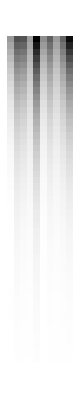

```mathematica
Dataset[NestList[step[#,0,-1]&,brain,50]][All,#"activation"&][ArrayPlot]
```

```mathematica
Dataset[NestList[step[#,0,-1]&,brain,100]][All,ArrayPlot[#"weights",PlotLegends->Automatic]&][ListAnimate]
```

How many changes between the state before and after:

```mathematica
Transpose[Dataset[{brain,step[brain,0,-1]}]][All,Length[Diff[ToString[Normal[#1]],ToString[Normal[#2]],"SummaryBox"]["Changes"]]&@@##&]
```

Reward = Random (Delirium): “If I feed the brain no sensory input but provide random reward, the existing weights fluctuate based on intermittent reinforcement of residual activity, neuron activations leak or flare up at the specified LeakRate, edges are pruned if the random fluctuation drops them below the SurvivalThreshold, and vertices whose residual activations coincidentally correlate are added sporadically at the specified SproutingRate within the capacities of the graph as specified by MaxDensity.”

2. Pattern (Input = 1)
Reward = 0 (Latent Learning): “If I feed the brain a consistent pattern but no reward, the existing weights don’t change, but neuron activations saturate to reflect the input, edges whose weights were already weak are maintained or pruned, and vertices whose strong activations correlate are added rapidly at the specified SproutingRate (forming ‘ghost’ connections) within the capacities of the graph as specified by MaxDensity.”

Reward = 1 (Imprinting): “If I feed the brain a consistent pattern and high reward, the existing weights grow rapidly toward saturation, neuron activations saturate to reflect the input, edges become strong and immune to pruning, and vertices whose activations correlate are added and immediately reinforced at the specified SproutingRate within the capacities of the graph as specified by MaxDensity.”

Reward = -1 (Aversion): “If I feed the brain a consistent pattern but provide negative reward, the existing weights connecting the pattern are actively decreased (anti-Hebbian), neuron activations saturate, edges are severed as they drop below the SurvivalThreshold, and sprouting is effectively cancelled as new connections are punished immediately within the capacities of the graph as specified by MaxDensity.”

Reward = Random (Robust Habit): “If I feed the brain a consistent pattern and random reward, the existing weights fluctuate but trend upward, neuron activations saturate, edges persist through droughts of reward, and vertices whose activations correlate are added at the specified SproutingRate creating resilient structures within the capacities of the graph as specified by MaxDensity.”

3. Inhibition (Input = -1)
Reward = 0 (Latent Inhibition): “If I feed the brain a negative (inhibitory) pattern and no reward, the existing weights don’t change, neuron activations saturate negatively, edges are maintained, and vertices whose inhibitions correlate (double-negative) are added at the specified SproutingRate within the capacities of the graph as specified by MaxDensity.”

Reward = 1 (Negative Imprinting): “If I feed the brain a negative (inhibitory) pattern and high reward, the existing weights between mutually inhibited neurons grow toward saturation, neuron activations saturate negatively, edges become strong, and vertices whose inhibitions correlate are added and reinforced at the specified SproutingRate within the capacities of the graph as specified by MaxDensity.”

Reward = -1 (Unlearning Absence): “If I feed the brain a negative (inhibitory) pattern and negative reward, the existing weights are actively decreased, neuron activations saturate negatively, edges between inhibited neurons are severed as they drop below the SurvivalThreshold, and sprouting is suppressed within the capacities of the graph as specified by MaxDensity.”

4. Noise (Input = Random)
Reward = 0 (Reservoir Generation): “If I feed the brain random noise and no reward, the existing weights don’t change, neuron activations flicker randomly, edges are maintained or pruned based on previous states, and vertices whose accidental noise spikes correlate are added at the specified SproutingRate creating a sparse reservoir within the capacities of the graph as specified by MaxDensity.”

Reward = 1 (Superstition): “If I feed the brain random noise and high reward, the existing weights jitter wildly as accidental coincidences are reinforced, neuron activations flicker, edges are pruned if the jitter drops them low, and vertices whose noise spikes correlate are added and reinforced at the specified SproutingRate, creating unstable ‘superstitious’ structures within the capacities of the graph as specified by MaxDensity.”

Reward = -1 (Whitening): “If I feed the brain random noise and negative reward, the existing weights decrease whenever accidental coincidences occur, neuron activations flicker, edges are pruned as they weaken, and sprouting is suppressed, leading to a sparser graph within the capacities of the graph as specified by MaxDensity.”

Reward = Random (Heat Death): “If I feed the brain random noise and random reward, the existing weights drift with high variance but zero net direction, neuron activations flicker, edges are pruned and sprouted chaotically at the specified SproutingRate with high turnover, resulting in an unstable topology within the capacities of the graph as specified by MaxDensity.”

If I feed it no sensory input, but give it a strong reward,

```mathematica
step[brain,0,1]
```

<|network→-Graphics-,weights→SparseArray[…],biases→0,activation→{-0.134457,-0.239974,0.232113,0.133646,-0.351235,-0.150498,-0.215552,-0.136474,0.21176,0.331413},sensorySensitivity→1,maxDensity→0.5,sensoryInput→0|>

```mathematica
(*Apply one step with zero sensory input and zero reward, so the only change is pruning edges that are under the weakness threshold*)
```

```mathematica
(*1. Verify Metabolic Decay (Input=0,Reward=0)*)(*Expectation:Activations (Blue) fade to 0. Weights (Orange) are flat.*)VerifyDecay[brain_,steps_:50]:=Module[{history,absAct,meanWeight},history=NestList[step[#,0,0]&,brain,steps];
(*Metrics*)absAct=Mean[Abs[#["activation"]]]&/@history;
meanWeight=Mean[Abs[Normal[#["weights"]]]]&/@history;
ListLinePlot[{absAct,meanWeight},PlotLegends->{"Mean |Activation| (Should Decay)","Mean |Weight| (Should be Const)"},PlotStyle->{Blue,{Orange,Dashed}},PlotLabel->"Scenario: Metabolic Decay (Silence)",Frame->True,ImageSize->Medium]];

(*2. Verify Hallucination (Input=0,Reward=1)*)
(*Expectation:Weights saturate to-1/1. Activations form stable stripes.*)
VerifyHallucination[brain_,steps_:50]:=Module[{history,weightsStart,weightsEnd},history=NestList[step[#,0,1]&,brain,steps];
weightsStart=Flatten[Normal[brain["weights"]]];
weightsEnd=Flatten[Normal[Last[history]["weights"]]];
Row[{ArrayPlot[Transpose[#["activation"]&/@history],PlotLabel->"Activation Raster (Time →)",FrameLabel->{"Neuron","Time"},AspectRatio->1/2,ImageSize->Medium],PairedHistogram[weightsStart,weightsEnd,PlotLabel->"Weight Distribution (Start vs End)",PlotLegends->{"Start","End"},ImageSize->Medium]}]];

(*3. Verify Aversion (Input=Pattern,Reward=-1)*)
(*Expectation:The specific pattern is punished.Edge count should drop as weights invert and prune.*)
VerifyAversion[brain_,steps_:50]:=Module[{history,pattern,edgeCounts},(*Create a random fixed pattern*)pattern=RandomInteger[1,Length[brain["activation"]]];
history=NestList[step[#,pattern,-1]&,brain,steps];
edgeCounts=EdgeCount[#["network"]]&/@history;
ListLinePlot[edgeCounts,PlotLabel->"Anatomical Pruning under Punishment (R = -1)",FrameLabel->{"Time","Edge Count"},PlotStyle->{Thick,Red},Filling->Bottom,ImageSize->Medium]];

(*4. Verify Density Cap (Input=Pattern,Reward=1)*)
(*Expectation:Even with max reward,Edge Count should hit a ceiling and stay flat (The Duel).*)
VerifyDensity[brain_,steps_:50]:=Module[{history,pattern,edgeCounts,limit},pattern=RandomInteger[1,Length[brain["activation"]]];
limit=Ceiling[brain["maxDensity"]*Length[brain["activation"]]^2];
history=NestList[step[#,pattern,1]&,brain,steps];
edgeCounts=EdgeCount[#["network"]]&/@history;
ListLinePlot[edgeCounts,PlotLabel->"Competitive Replacement (The Duel)",FrameLabel->{"Time","Edge Count"},GridLines->{None,{limit}},Epilog->{Dashed,Line[{{0,limit},{steps,limit}}],Text["MaxDensity",{5,limit+1}]},PlotRange->All,ImageSize->Medium]];
```

### Experiment: Pavlovian Conditioning

Let’s make a new brain with 10 neurons from a Barabasi Albert graph with edges added 3 at a time. It’s important that the two neurons we are conditioning are structurally disconnected on the neural network

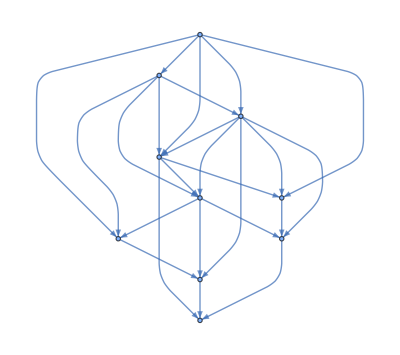
<|network→-Graphics-,weights→SparseArray[…],biases→0,activation→{-0.0732533,-0.152863,-0.340631,-0.0966331,-0.245857,-0.318132,-0.186101,0.0762134,-0.206941,0.247269},sensorySensitivity→1,sensoryInput→0,maxDensity→0.5|>

```mathematica
ClearAll[brain]
(*Initialize a brain with a Barabasi Albert graph with the specified parameters:*)
brain=With[{n=10,k=3,τ=.005},
neuralNet[
(*Generate a Barabasi Albert graph with the chosen parameters:*)
RandomGraph[BarabasiAlbertGraphDistribution[n,k]]//
(*Convert edges to directed edges and indexed vertices::*)
(Graph[Sort[VertexList[#]],MapApply[DirectedEdge,#]]&@EdgeList[#]&)//
(*Delete any existing edges between node 1 and node n:*)
EdgeDelete[#,_?(MatchQ[#,1->n|n->1]&)]&
]]
```

Baseline: We feed the brain nothing

Baseline/control: We feed the brain random noise for 20 ticks, with no reward.

<|network→-Graphics-,weights→SparseArray[…],biases→0,activation→{-0.00751166,-0.0196582,-0.041243,-0.0161226,-0.0271448,-0.0362569,-0.0230351,0.00726004,-0.0274008,0.0300622},sensorySensitivity→1,maxDensity→0.5,sensoryInput→0|>

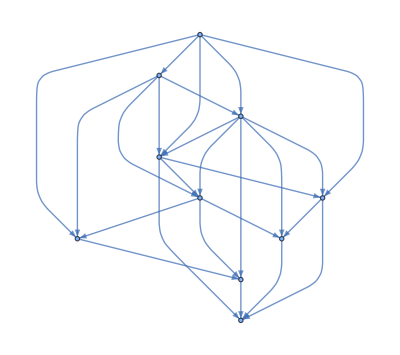
<|network→-Graphics-,weights→SparseArray[…],biases→0,activation→{0.632598,0.654972,0.610383,0.65286,0.639109,0.621897,0.645008,0.68422,0.636254,0.699064},sensorySensitivity→1,maxDensity→0.5,sensoryInput→1|>

<|network→-Graphics-,weights→SparseArray[…],biases→0,activation→{0.401028,0.426904,0.379595,0.422583,0.411246,0.392718,0.416143,0.456144,0.406046,0.47051},sensorySensitivity→1,maxDensity→0.5,sensoryInput→0.468496|>

<|network→-Graphics-,weights→SparseArray[…],biases→0,activation→{0.402832,0.448531,0.244446,0.363097,0.304805,0.333002,0.40239,0.291247,0.294597,0.370212},sensorySensitivity→1,maxDensity→0.5,sensoryInput→{0.970007,0.352166,0.072663,0.519005,0.455844,0.061822,0.559961,0.144906,0.385047,0.15395}|>

```mathematica
Nest[step[#1,0,0]&,brain,20]
Nest[step[#1,1,0]&,brain,20]
Nest[step[#1,RandomReal[],0]&,brain,20]
Nest[step[#1,RandomReal[1,VertexCount[brain["network"]]],0]&,brain,20]
```

```mathematica
(*With[{baselineBrain=Nest[step[#1,RandomReal[1,VertexCount[brain["network"]]],1]&,brain,100]},
baselineBrain
]*)
```

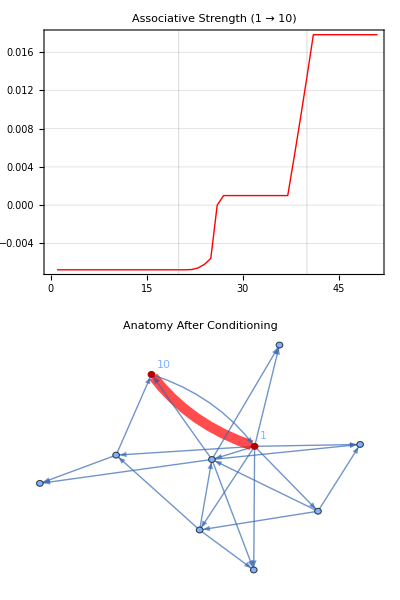

```mathematica
Module[{n=10,g,brain,inputsA,inputsB,inputsC,allInputs,rewardsA,rewardsB,rewardsC,allRewards,history,weightPath,finalGraph},(*1. SETUP:Lobotomized Brain*)
(*Define the starting network:*)
g=RandomGraph[BarabasiAlbertGraphDistribution[n,3]];
g=EdgeDelete[g,_?(MatchQ[#,1->n|n->1]&)];
g=Graph[Range[n],DirectedEdge@@@EdgeList[g],VertexSize->Large];
(*Define the initial network association:*)
brain=neuralNet[g];
(*PROTOCOL*)
(*Phase A:Baseline (20 ticks)-Noise*)
inputsA=RandomReal[{0,0.1},{20,n}];
rewardsA=ConstantArray[0,20];
(*Phase B:Conditioning (20 ticks)-Force 1& N,Reward*)
inputsB=Table[ReplacePart[ConstantArray[0.,n],{1->1.0,n->1.0}]+RandomReal[{-0.05,0.05},n],{20}];
rewardsB=ConstantArray[1,20];
(*Phase C:Testing (10 ticks)-Pulse 1 only,No Reward*)
inputsC=Table[ReplacePart[ConstantArray[0.,n],{1->1.0}],{10}];
rewardsC=ConstantArray[0,10];
(*Combine*)allInputs=Join[inputsA,inputsB,inputsC];
allRewards=Join[rewardsA,rewardsB,rewardsC];
(*EXECUTE*)history=FoldList[step[#1,#2[[1]],#2[[2]]]&,brain,Transpose[{allInputs,allRewards}]];
(*VISUALIZE*)weightPath=Map[#["weights"][[1,n]]&,history];
finalGraph=history[[40]]["network"];
Column[{ListLinePlot[weightPath,PlotLabel->"Associative Strength (1 → "<>ToString[n]<>")",Frame->True,GridLines->{{20,40},Automatic},PlotStyle->{Thick,Red},ImageSize->Medium],HighlightGraph[finalGraph,{1,n},VertexLabels->"Name",EdgeStyle->{(1->n)->{Red,Thickness[0.02]}},PlotLabel->"Anatomy After Conditioning",ImageSize->Medium]}]]
```

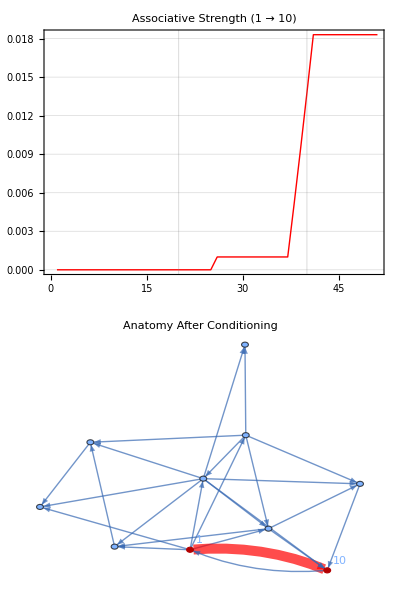

```mathematica
SeedRandom[0];
Module[{n=10,g,brain,inputsA,inputsB,inputsC,allInputs,rewardsA,rewardsB,rewardsC,allRewards,history,weightPath,finalGraph},(*1. SETUP:Lobotomized Brain*)
(*Define the starting network:*)
g=RandomGraph[BarabasiAlbertGraphDistribution[n,3]];
g=EdgeDelete[g,_?(MatchQ[#,1->n|n->1]&)];
g=Graph[Range[n],DirectedEdge@@@EdgeList[g],VertexSize->Large];
(*Define the initial network association:*)
brain=neuralNet[g];
(*PROTOCOL*)
(*Phase A:Baseline (20 ticks)-Noise*)
inputsA=RandomReal[{0,0.1},{20,n}];
rewardsA=ConstantArray[0,20];
(*Phase B:Conditioning (20 ticks)-Force 1& N,Reward*)
inputsB=Table[ReplacePart[ConstantArray[0.,n],{1->1.0,n->1.0}]+RandomReal[{-0.05,0.05},n],{20}];
rewardsB=ConstantArray[1,20];
(*Phase C:Testing (10 ticks)-Pulse 1 only,No Reward*)
inputsC=Table[ReplacePart[ConstantArray[0.,n],{1->1.0}],{10}];
rewardsC=ConstantArray[0,10];
(*Combine*)allInputs=Join[inputsA,inputsB,inputsC];
allRewards=Join[rewardsA,rewardsB,rewardsC];
(*EXECUTE*)history=FoldList[step[#1,#2[[1]],#2[[2]]]&,brain,Transpose[{allInputs,allRewards}]];
(*VISUALIZE*)weightPath=Map[#["weights"][[1,n]]&,history];
finalGraph=history[[40]]["network"];
Column[{ListLinePlot[weightPath,PlotLabel->"Associative Strength (1 → "<>ToString[n]<>")",Frame->True,GridLines->{{20,40},Automatic},PlotStyle->{Thick,Red},ImageSize->Medium],HighlightGraph[finalGraph,{1,n},VertexLabels->"Name",EdgeStyle->{(1->n)->{Red,Thickness[0.02]}},PlotLabel->"Anatomy After Conditioning",ImageSize->Medium]}]]
```

```mathematica
SeedRandom[0];
Module[{n=10,g,brain,inputsA,inputsB,inputsC,allInputs,rewardsA,rewardsB,rewardsC,allRewards,history,weightPath,finalGraph},(*1. SETUP:Lobotomized Brain*)
(*Define the starting network:*)
g=RandomGraph[BarabasiAlbertGraphDistribution[n,3]];
g=EdgeDelete[g,_?(MatchQ[#,1->n|n->1]&)];
g=Graph[Range[n],DirectedEdge@@@EdgeList[g],VertexSize->Large];
(*Define the initial network association:*)
brain=neuralNet[g];
(*PROTOCOL*)
(*Phase A:Baseline (20 ticks)-Noise*)inputsA=RandomReal[{0,0.1},{20,n}];
rewardsA=ConstantArray[0,20];
(*Phase B:Conditioning (20 ticks)-Force 1& N,Reward*)inputsB=Table[ReplacePart[ConstantArray[0.,n],{1->1.0,n->1.0}]+RandomReal[{-0.05,0.05},n],{20}];
rewardsB=ConstantArray[1,20];
(*Phase C:Testing (10 ticks)-Pulse 1 only,No Reward*)inputsC=Table[ReplacePart[ConstantArray[0.,n],{1->1.0}],{10}];
rewardsC=ConstantArray[0,10];
(*Combine*)allInputs=Join[inputsA,inputsB,inputsC];
allRewards=Join[rewardsA,rewardsB,rewardsC];
(*EXECUTE*)history=FoldList[step[#1,#2[[1]],#2[[2]]]&,brain,Transpose[{allInputs,allRewards}]];
(*VISUALIZE*)weightPath=Map[#["weights"][[1,n]]&,history];
history[[All,"network"]]]//ListAnimate
```

## Virtual embodiment TODO

#### particles in an agar.io-like world eating each other; the particles get more neurons k at a time if they eat, but lose neurons if they are eaten; the particles are minimally embodied: they can sense the environment, navigate it, and eat; the particles that become most successful will be the ones that learn to eat each other and take advantage of the environmental constraints and the behaviours of the other particlles.

Define a list of microbes:

```mathematica
organisms=Range[10];
```

Define a list of microbe sizes:

```mathematica
sizes=RandomReal[1,10];
```

Define a list of microbe positions:

```mathematica
positions=RandomPoint[Disk[],10];
```

```mathematica
Transpose@Dataset@AssociationThread[{"id","size","position"},{organisms,sizes,positions}]
```

each neuron contributes on unit size

Define the interaction between two individual microbes:

```mathematica
particleInteraction[{size1_,position1_},{size2_,position2_}]:=If[EuclideanDistance[position1,position2]>
```

```mathematica
a
```

a